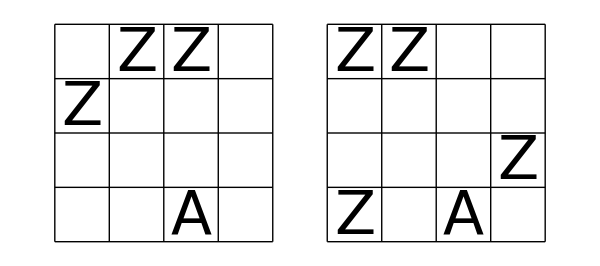

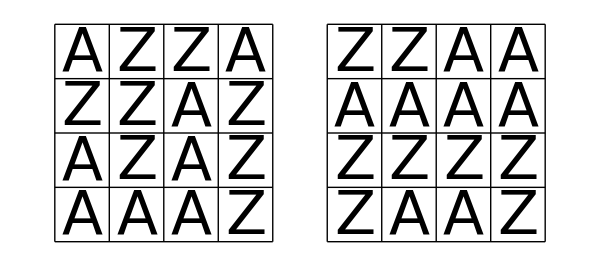

```mathematica
a=Flatten[Outer[List,{0,1},{0,1},{0,1},{0,1}],3];
```

```mathematica
b=Flatten[Outer[List,a,a,a,a,1],3];
```

```mathematica
rac[L_]:=L~Join~Transpose[L]
```

```mathematica
c=Select[b,Length[Union[rac[#]]]==8&];
```

```mathematica
Length[c]
```

6840

```mathematica
solns={};
For[i=1,i≤6840,i++,
f1=c[[i]];
r1=rac[f1];
solns=solns~Join~Map[{f1,#}&,Select[c,Length[Union[rac[#]~Join~r1]]==16&]]];
```

```mathematica
Length[solns]
```

17664

```mathematica
g[L_]:=Module[{j},
M=solns;
For[j=1,j≤Length[L],j++,
t=L[[j]];
M=Select[M,#[[Apply[Sequence,Take[t,3]]]]==Last[t]&]];
M]
```

```mathematica
beforepic[L_]:=Graphics[Style[{Table[Line[{{0,i},{4,i}}],{i,0,4}],Table[Line[{{i,0},{i,4}}],{i,0,4}],Table[Line[{{5,i},{9,i}}],{i,0,4}],Table[Line[{{i,0},{i,4}}],{i,5,9}],Map[Text[If[#[[4]]==0,Style["A",FontSize->14],Style["Z",FontSize->14]],{5#[[1]]+#[[2]]-5.5,4.45-#[[3]]}]&,L]
},Antialiasing->False],ImageSize->150]
```

```mathematica
afterpic[L_]:=Graphics[Style[{Table[Line[{{0,i},{4,i}}],{i,0,4}],Table[Line[{{i,0},{i,4}}],{i,0,4}],Table[Line[{{5,i},{9,i}}],{i,0,4}],Table[Line[{{i,0},{i,4}}],{i,5,9}],MapIndexed[Text[If[#1==0,Style["A",FontSize->14],Style["Z",FontSize->14]],{5#2[[1]]+#2[[2]]-5.5,4.45-#2[[3]]}]&,L,{3}]
},Antialiasing->False],ImageSize->150]
```

```mathematica
For[k=1,k>0,k++,
P=solns;
con={};
While[Length[P]>1,
AppendTo[con,{RandomInteger[{1,2}],RandomInteger[{1,4}],RandomInteger[{1,4}],RandomInteger[{0,1}]}];
P=g[con]];
If[Length[P]==1,
For[kk=1,kk≤Length[con],kk++,
gg=g[Drop[con,{kk}]];
If[Length[gg]==1,con=Drop[con,{kk}];kk--]];
If[Length[con]≤9,
Print[Length[con]];Print[beforepic[con]];Print[afterpic[P[[1]]]]]]]
```

## 9

9

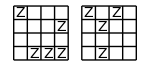

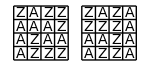

9

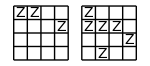

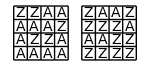

9

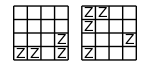

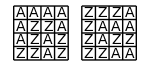

9

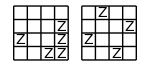

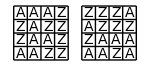

9

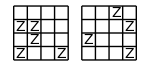

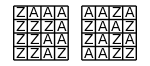

9

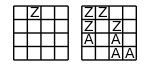

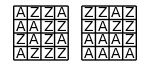

9

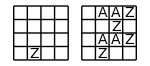

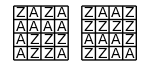

9

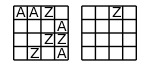

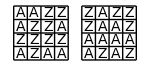

9

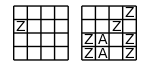

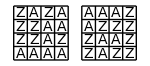

9

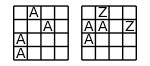

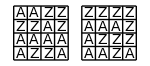

9

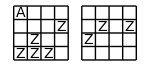

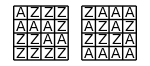

9

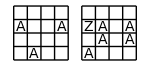

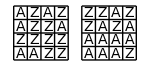

9

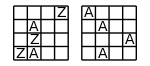

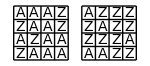

9

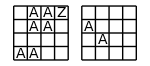

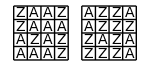

9

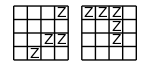

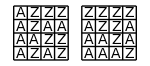

9

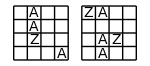

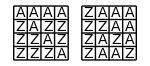

9

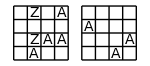

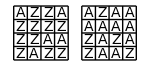

9

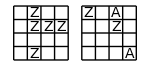

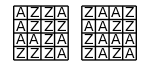

9

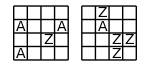

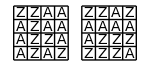

9

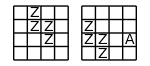

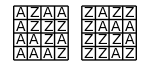

9

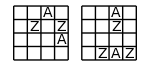

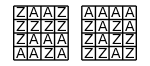

9

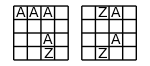

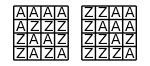

9

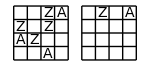

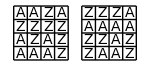

9

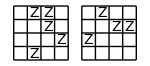

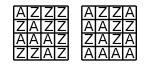

9

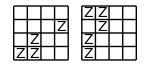

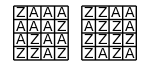

9

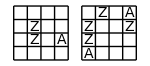

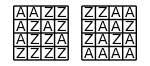

9

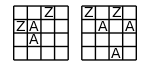

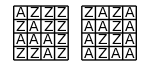

9

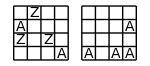

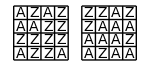

## 8

8

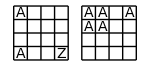

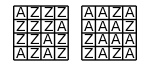

8

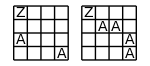

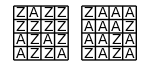

8

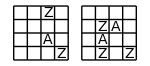

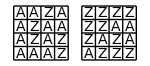

8

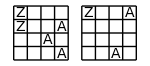

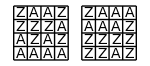

8

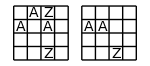

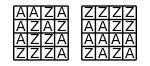

8

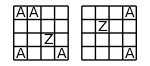

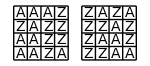

8

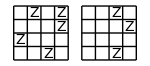

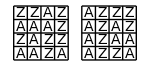

8

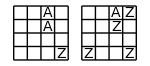

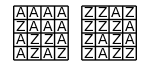

8

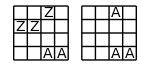

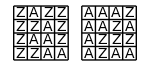

8

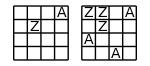

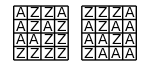

8

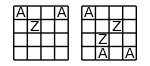

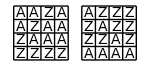

8

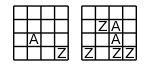

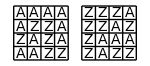

8

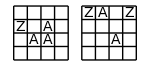

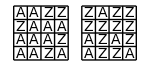

8

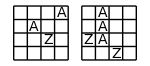

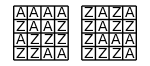

8

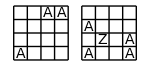

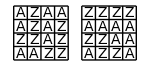

8

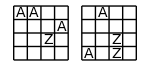

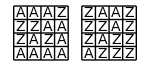

8

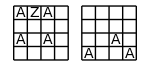

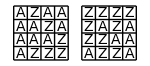

8

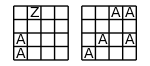

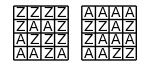

8

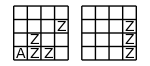

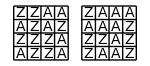

8

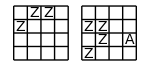

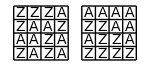

8

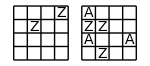

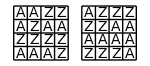

8

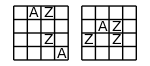

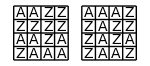

8

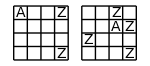

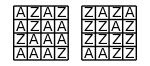

8

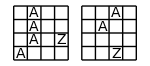

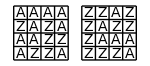

8

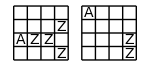

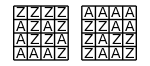

8

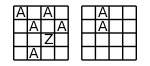

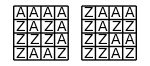

8

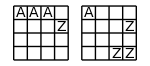

-Graphics-

8

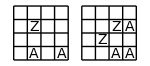

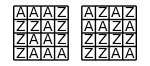

8

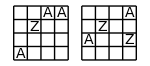

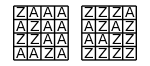

8

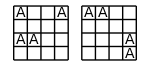

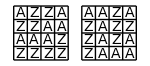

8

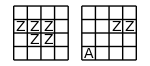

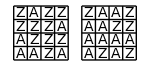

8

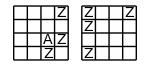

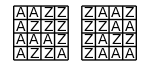

8

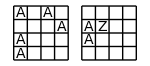

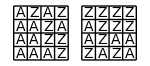

8

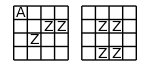

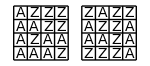

8

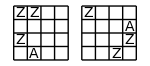

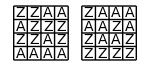

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

8

-Graphics-

-Graphics-

## 7

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-

7

-Graphics-

-Graphics-